```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory@NotebookDirectory[], "data"}]]
```

/Users/arsenytokarev/Desktop/CourseWorks/Gas Dynamics/Code/data

```mathematica
NormalRepresentation[data_List]:= Module[
{solution, mesh},
solution = {ToExpression@#⟦1⟧, #⟦2⟧} &/@ data;
For[i =1, i <= Length@solution, ++i,
 solution⟦i,2⟧ = {ToExpression@#⟦1⟧, ToExpression@#⟦2⟧} &/@ solution⟦i,2⟧
];
Return[Sort@solution]
];
```

```mathematica
Plots[data_List]:= ListPlot[#⟦2⟧ &/@ data, PlotRange->All, ImageSize->800, GridLines->Automatic, Ticks->{Table[i, {i, 0, 200, 20}], {0, 1}}]
```

## Точные решения

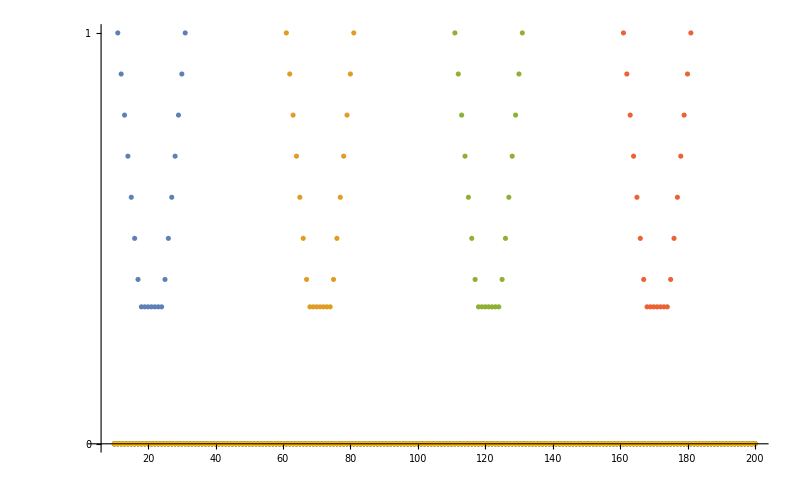

```mathematica
advection = NormalRepresentation@Import["advection.json"] ;
Plots[advection]
```

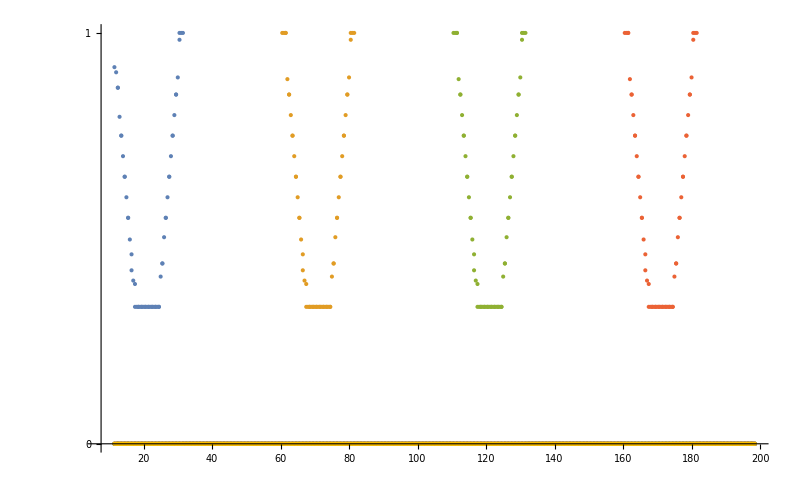

```mathematica
advectionPPM = NormalRepresentation@Import["advectionPPM.json"] ;
ppmPlot =Plots[advectionPPM]
```

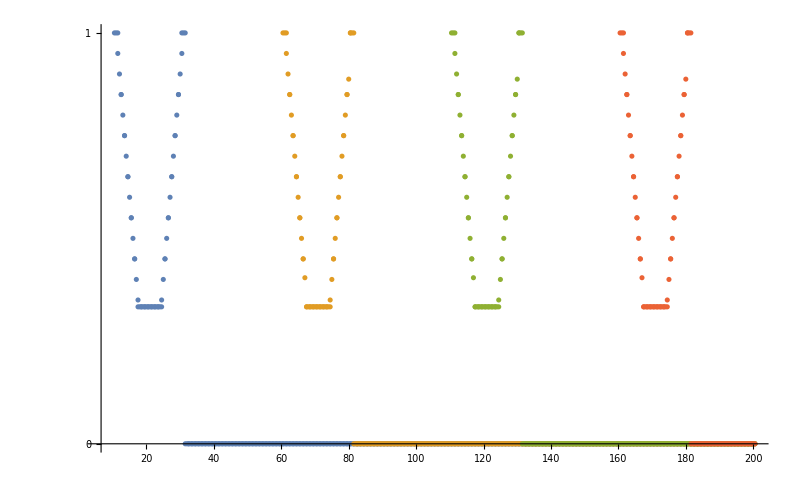

```mathematica
advectionPPML = NormalRepresentation@Import["advectionPPML.json"] ;
ppmlPlot = Plots[advectionPPML]
```

```mathematica
If[!True ,
FileExport[ppmPlot, "advection_ppm.pdf", "PDF"];
FileExport[ppmlPlot, "advection_ppml.pdf", "PDF"];
];
```

```mathematica
Sort@advection⟦1,2, 1;;23⟧
```

{{10.,0.},{11.,1.},{12.,0.9},{13.,0.8},{14.,0.7},{15.,0.6},{16.,0.5},{17.,0.4},{18.,0.333333},{19.,0.333333},{20.,0.333333},{21.,0.333333},{22.,0.333333},{23.,0.333333},{24.,0.333333},{25.,0.4},{26.,0.5},{27.,0.6},{28.,0.7},{29.,0.8},{30.,0.9},{31.,1.},{32.,0.}}

```mathematica
Sort@advectionPPML⟦1,2, 1;;70⟧
```

{{10.5,1.},{11.,1.},{11.5,1.},{11.5,0.95},{12.,0.9},{12.5,0.85},{12.5,0.85},{13.,0.8},{13.5,0.75},{13.5,0.75},{14.,0.7},{14.5,0.65},{14.5,0.65},{15.,0.6},{15.5,0.55},{15.5,0.55},{16.,0.5},{16.5,0.45},{16.5,0.45},{17.,0.4},{17.5,0.35},{17.5,0.333333},{18.,0.333333},{18.5,0.333333},{18.5,0.333333},{19.,0.333333},{19.5,0.333333},{19.5,0.333333},{20.,0.333333},{20.5,0.333333},{20.5,0.333333},{21.,0.333333},{21.5,0.333333},{21.5,0.333333},{22.,0.333333},{22.5,0.333333},{22.5,0.333333},{23.,0.333333},{23.5,0.333333},{23.5,0.333333},{24.,0.333333},{24.5,0.333333},{24.5,0.35},{25.,0.4},{25.5,0.45},{25.5,0.45},{26.,0.5},{26.5,0.55},{26.5,0.55},{27.,0.6},{27.5,0.65},{27.5,0.65},{28.,0.7},{28.5,0.75},{28.5,0.75},{29.,0.8},{29.5,0.85},{29.5,0.85},{30.,0.9},{30.5,0.95},{30.5,1.},{31.,1.},{31.5,1.},{31.5,0.},{32.,0.},{32.5,0.},{32.5,0.},{33.,0.},{33.5,0.},{33.5,0.}}

```mathematica
Sort@advectionPPM⟦2,2, 148;;218⟧
```

{{60.5,1.},{61.,1.},{61.5,1.},{61.5,1.},{62.,0.8875},{62.5,0.85},{62.5,0.85},{63.,0.8},{63.5,0.75},{63.5,0.75},{64.,0.7},{64.5,0.65},{64.5,0.65},{65.,0.6},{65.5,0.55},{65.5,0.55},{66.,0.497222},{66.5,0.461111},{66.5,0.422222},{67.,0.397222},{67.5,0.388889},{67.5,0.333333},{68.,0.333333},{68.5,0.333333},{68.5,0.333333},{69.,0.333333},{69.5,0.333333},{69.5,0.333333},{70.,0.333333},{70.5,0.333333},{70.5,0.333333},{71.,0.333333},{71.5,0.333333},{71.5,0.333333},{72.,0.333333},{72.5,0.333333},{72.5,0.333333},{73.,0.333333},{73.5,0.333333},{73.5,0.333333},{74.,0.333333},{74.5,0.333333},{74.5,0.333333},{75.,0.406944},{75.5,0.438889},{75.5,0.438889},{76.,0.502778},{76.5,0.55},{76.5,0.55},{77.,0.6},{77.5,0.65},{77.5,0.65},{78.,0.7},{78.5,0.75},{78.5,0.75},{79.,0.8},{79.5,0.85},{79.5,0.85},{80.,0.891667},{80.5,0.983333},{80.5,1.},{81.,1.},{81.5,1.},{81.5,0.},{82.,0.},{82.5,0.},{82.5,0.},{83.,0.},{83.5,0.},{83.5,0.},{84.,0.}}